Create a function that takes into account 
1. whether the point starts on left or right wall (0,1) and where on the y-axis it is (a) --> (0 or 1, a)
2. whether the point is going up or down the billiard
3. (eventually) if the slope is greater than 1 (goes to the ceiling)

```mathematica
(*Table[{((-1)^(k+1)+1)/2, -km}, {k, 1, n}]*)

(* to find n *)
(*n = Floor[(1-a)/m]*)

(* if the point starts at 0, then a = 0 *)
```

{{0,0}}

n: 3

uppts: {{1,3/7},{0,6/7}}

initial pts: {{0,0}}

pts after Join: {{0,0},{1,3/7},{0,6/7}}

i: 3

hi again:

a:5/7

down pts:{{0,3/7}}

Final pts:{{0,0},{1,3/7},{0,6/7},{1/3,1},{1,5/7},{0,3/7}}

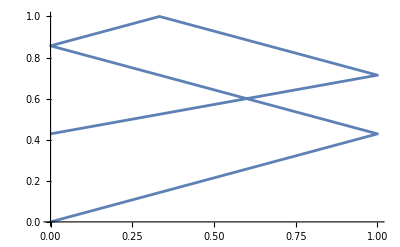

```mathematica
pts = {{0,0}};
(* Take into account that k changes from postitive to negative and from odd and even *)

(* call the billiard function everytime the ball hits a wall *)
mathematicalBiliard[m_,dist_]:=

Module[{n,uppts,i},
n=Ceiling[(1)/m];
Print["n: ", n]; (*debugging*)

uppts=Table[{((-1)^(k-1)+1)/2, k*m},{k,1,n-1}];
Print["uppts: ", uppts]; (*debugging*)
Print["initial pts: ", pts];

pts=Join[pts,uppts];
Print["pts after Join: ", pts]; (*debugging*)
i=n;
If[i==n,
Print["i: ", i]; 
If[Mod[i,2]==0,(*even, we have to fix this*)
Print["hi: ", i]; pts=Append[pts,{(m*pts[[i]][[1]]-pts[[i]][[2]])/m,1}];
];
If[Mod[i,2]!=0,(*odd*)
Print["hi again: "]; tpts={{(1-m*pts[[i]][[1]]-pts[[i]][[2]])/m,1}};
pts=Join[pts,tpts];
i++;
ntpts = {{1, -m*(1-pts[[i]][[1]]) + pts[[i]][[2]]}};
pts=Join[pts,ntpts];];
i++;
];(*this works*);

a=pts[[i]][[2]];
p=Ceiling[(1-a)/m];
repeats=n+p;
Print["a:", a];
downpts =Table[{(1-(-1)^(k+1))/2, k (m)}, {k, 1, p}] ;
Print["down pts:", downpts];
pts= Join[pts, downpts];
i= repeats;
(*here is the math for off the bottom*);
Print["Final pts:", pts]; (*debugging*)
Return[pts];]
Print["wtf:"pts];
pts= mathematicalBiliard[m= 3/7,dist=5];
ListLinePlot[pts]

(*ask: does this need to be two functions, or can we leave it at 1, and call while i<= dist?
*)
```